# A flux-based approach for analyzing the disguised toric locus of reaction networks

Balázs Boros^(1,2), Gheorghe Craciun^(3,4), Oskar Henriksson^5, Jiaxin Jin^6, Diego Rojas La Luz^3

1 Bolyai Institute, University of Szeged, Hungary
2 National Laboratory for Health Security, University of Szeged, Hungary
3 Department of Mathematics, University of Wisconsin-Madison, United States
4 Department of Biomolecular Chemistry, University of Wisconsin-Madison, United States
5 Max Planck Institute of Molecular Cell Biology and Genetics, Dresden, Germany
6 Department of Mathematics, University of Louisiana at Lafayette, United States

This file contains the calculations that appear in Section 7 in the paper titled  “A flux-based approach for analyzing the disguised toric locus of reaction networks.”

## Modules

We collect some modules that are used below.

```mathematica
GetMassAction[reactions_]:=Module[{n,G,rates,flux,vars,srcs,tgts,monomials,f},
G=Graph[reactions];
n=Length[reactions[[1,1]]];
rates=Table[Subscript[κ, i],{i,1,Length[reactions]}];
flux=Table[Subscript[β, i],{i,1,Length[reactions]}];
vars=Switch[n,2,{x,y},3,{x,y,z},4,{x,y,z,w},_,Table[Subscript[x, i],{i,1,n}]];
srcs=EdgeList[G][[All,1]];
tgts=EdgeList[G][[All,2]];
monomials=rates*Apply[Times,vars^srcsᵀ];
f=Total[monomials*(tgts-srcs)];
{f,rates,G,monomials,vars,flux}
];

GetEQ[reactions_]:=Module[{f,vars,all1,EQUIL,i},
{f,vars}=GetMassAction[reactions][[{1,5}]];
all1=Table[vars[[i]]->1,{i,1,Length[vars]}];
EQUIL=(f/.{κ->β}/.all1)==0;
EQUIL
];

GetFlux[reactions_]:=Module[{},
GetMassAction[reactions][[6]]
];

GetDEandVB[rxnG_,rxnH_]:=Module[{f1,vars1,f2,rates2,G2,flux2,DE,VB},
{f1,vars1}=GetMassAction[rxnG][[{1,5}]];
{f2,rates2,G2}=GetMassAction[rxnH][[{1,2,3}]];
flux2=rates2/.{κ->γ};
DE=CoefficientList[(f1/.{κ->β})-(f2/.{κ->γ}),vars1]==0;
VB=IncidenceMatrix[G2].flux2==0;
{DE,VB}
];

Getβ2κ[reactions_]:=Module[{flux,monomials,β2κ,vars,κs,i},
flux=GetFlux[reactions];
{κs,monomials,vars}=GetMassAction[reactions][[{2,4,5}]];
β2κ=Table[flux[[i]]->monomials[[i]],{i,1,Length[reactions]}];
{β2κ,κs,vars}
];

DrawEGraph[rxn_]:=Module[{},{
Graph[rxn,VertexCoordinates->Table[i->i,{i,VertexList[rxn]}],ImageSize->Tiny]
}];
```

## Examples

## Example 2.17

We verify that the Horn-Jackson function is indeed not always a global Lyapunov function for the partly reversible square.
We find that the value of the Horn-Jackson can both increase and decrease along trajectories in any neighborhood of the equilibrium, provided  is chosen accordingly.
The equilibrium is a saddle of the function  for those specific rate constants.

```mathematica
gradL=Log[{Subscript[x, 1],Subscript[x, 2]}];
f={Subscript[κ, 1](1-Subscript[x, 1] Subscript[x, 2]),Subscript[κ, 2](Subscript[x, 1]-Subscript[x, 2])+Subscript[κ, 1](1-Subscript[x, 1] Subscript[x, 2])};
H=D[gradL.f,{{Subscript[x, 1],Subscript[x, 2]},2}]/.{Subscript[x, 1]->1,Subscript[x, 2]->1};
Print["Hessian matrix: ",MatrixForm[H]];
Print["determinant of the Hessian matrix is negative for ",Reduce[Det[H]<0&&Subscript[κ, 1]>0&&Subscript[κ, 2]>0]];
```

Hessian matrix: (-2 κ_1 | -2 κ_1+κ_2
-2 κ_1+κ_2 | 2 (-κ_1-κ_2))

determinant of the Hessian matrix is negative for κ_1>0&&κ_2>8 κ_1

## 7.1 Reversible square

```mathematica
rxnG={{0,0}->{1,0},{1,0}->{1,1},{1,1}->{0,1},{0,1}->{0,0},{1,0}->{0,0},{1,1}->{1,0},{0,1}->{1,1},{0,0}->{0,1}};
DrawEGraph[rxnG][[1]]
```

-Graphics-

### Equilibrium fluxes

```mathematica
EQ=GetEQ[rxnG]
```

{β_1-β_3-β_5+β_7,β_2-β_4-β_6+β_8}==0

### Disguised toric flux cone

```mathematica
rxnH=Join[rxnG,{{0,0}->{1,1},{1,1}->{0,0},{1,0}->{0,1},{0,1}->{1,0}}]; (*  *)
{DE,VB}=GetDEandVB[rxnG,rxnH];
sol=Solve[DE&&VB,{Subscript[β, 1],Subscript[β, 8],Subscript[γ, 1],Subscript[γ, 2],Subscript[γ, 3],Subscript[γ, 4],Subscript[γ, 5],Subscript[γ, 6],Subscript[γ, 7],Subscript[γ, 8],Subscript[γ, 9]}][[1]];
MatrixForm[sol]
```

(β_1→β_3+β_5-β_7
β_8→-β_2+β_4+β_6
γ_1→β_2+β_5-β_6+γ_10-γ_11-γ_12
γ_2→β_2-γ_11
γ_3→β_3-γ_10
γ_4→β_4-γ_12
γ_5→β_5-γ_11
γ_6→β_6-γ_10
γ_7→β_7-γ_12
γ_8→-β_3+β_4+β_7+γ_10-γ_11-γ_12
γ_9→-β_2+β_3+β_6-β_7-γ_10+γ_11+γ_12)

Next, we verify that the simplified formula is indeed equivalent to what we originally got.

```mathematica
flux=GetFlux[rxnG];
disgβ1=Max[Subscript[β, 1],Subscript[β, 8]]-Subscript[β, 4]-Subscript[β, 5]<=Min[Subscript[β, 3],Subscript[β, 6]]&&-Min[Subscript[β, 2],Subscript[β, 5]]-Min[Subscript[β, 4],Subscript[β, 7]]<=Subscript[β, 1]-Subscript[β, 5]-Subscript[β, 2]+Subscript[β, 6]&&EQ&&flux>0;
disgβ2=(Subscript[β, 1]-Subscript[β, 8])(Subscript[β, 3]-Subscript[β, 6])<=(Subscript[β, 2]+Subscript[β, 5])(Subscript[β, 4]+Subscript[β, 7])&&(Subscript[β, 2]-Subscript[β, 5])(Subscript[β, 4]-Subscript[β, 7])<=(Subscript[β, 1]+Subscript[β, 8])(Subscript[β, 3]+Subscript[β, 6])&&EQ&&flux>0;
Reduce[disgβ1&&Not[disgβ2]]
Reduce[Not[disgβ1]&&disgβ2]
```

False

False

### Disguised toric locus

How much of the simplex is covered by the disguised toric locus? We get approximately 83.3%
(1 million simulations take about 25 seconds.)

```mathematica
M=1000000;
count=0;
disgκ=(Subscript[κ, 1]-Subscript[κ, 8])(Subscript[κ, 3]-Subscript[κ, 6])<=(Subscript[κ, 2]+Subscript[κ, 5])(Subscript[κ, 4]+Subscript[κ, 7])&&(Subscript[κ, 2]-Subscript[κ, 5])(Subscript[κ, 4]-Subscript[κ, 7])<=(Subscript[κ, 1]+Subscript[κ, 8])(Subscript[κ, 3]+Subscript[κ, 6]);
For[i=1,i<=M,i++,{
rnd=RandomVariate[ExponentialDistribution[1],8];
If[disgκ/.Table[Subscript[κ, j]->rnd[[j]],{j,1,8}],count++];
}];
Print[N[100count/M,3],"% of the simplex is covered by K^dt(G)"];
```

83.3% of the simplex is covered by K^dt(G)

## 7.2 Square vs. parallelogram

```mathematica
rxnG={{0,1}->{1,0},{1,0}->{1,2},{1,2}->{0,3},{0,3}->{0,1},{1,2}->{1,0},{0,1}->{0,3}};
DrawEGraph[rxnG][[1]]
```

-Graphics-

```mathematica
rxnG={{0,0}->{1,0},{1,0}->{1,1},{1,1}->{0,1},{0,1}->{0,0},{1,1}->{1,0},{0,0}->{0,1}};
DrawEGraph[rxnG][[1]]
```

-Graphics-

### Equilibrium fluxes

```mathematica
EQ=GetEQ[rxnG]
```

{β_1-β_3,β_2-β_4-β_5+β_6}==0

### Disguised toric flux cone

```mathematica
rxnH=Join[rxnG,{{0,0}->{1,1},{1,1}->{0,0}}];
{DE,VB}=GetDEandVB[rxnG,rxnH];
sol=Solve[DE&&VB,{Subscript[β, 2],Subscript[β, 3],Subscript[γ, 1],Subscript[γ, 2],Subscript[γ, 3],Subscript[γ, 4],Subscript[γ, 5],Subscript[γ, 6],Subscript[γ, 7]}][[1]];
MatrixForm[sol]
```

(β_2→β_4+β_5-β_6
β_3→β_1
γ_1→β_4-β_6+γ_8
γ_2→β_4+β_5-β_6
γ_3→β_1-γ_8
γ_4→β_4
γ_5→β_5-γ_8
γ_6→-β_1+β_4+γ_8
γ_7→β_1-β_4+β_6-γ_8)

Next, we verify that the simplified formula is indeed equivalent to what we originally got.

```mathematica
flux=GetFlux[rxnG];
disgβ1=Max[Subscript[β, 1],Subscript[β, 6]]-Subscript[β, 4]<=Min[Subscript[β, 1],Subscript[β, 5],Subscript[β, 1]+Subscript[β, 6]-Subscript[β, 4]]&&Subscript[β, 1]+Subscript[β, 6]-Subscript[β, 4]>=0&&EQ&&flux>0;
disgβ2=Abs[Subscript[β, 4]-Subscript[β, 6]]<=Subscript[β, 1]<=Subscript[β, 4]+Subscript[β, 5]&&EQ&&flux>0;
Reduce[disgβ1&&Not[disgβ2]]
Reduce[Not[disgβ1]&&disgβ2]
```

False

False

### Disguised toric locus

```mathematica
{β2κ,κs,vars}=Getβ2κ[rxnG];
disgκ1=Reduce[Resolve[Exists[{x,y},(disgβ2/.β2κ)&&κs>0&&vars>0]]];
disgκ2=(1-Subscript[κ, 6]/Subscript[κ, 1])(1-Subscript[κ, 5]/Subscript[κ, 3])<=(Subscript[κ, 2] Subscript[κ, 4])/(Subscript[κ, 1] Subscript[κ, 3])<=(1+Subscript[κ, 6]/Subscript[κ, 1])(1+Subscript[κ, 5]/Subscript[κ, 3])&&κs>0;
Reduce[disgκ1&&Not[disgκ2]]
Reduce[Not[disgκ1]&&disgκ2]
```

False

False

How much of the simplex is covered by the disguised toric locus? We get approximately 58.3%
(1 million simulations take about 25 seconds.)

```mathematica
M=1000000;
count=0;
disgκ=(1-Subscript[κ, 6]/Subscript[κ, 1])(1-Subscript[κ, 5]/Subscript[κ, 3])<=(Subscript[κ, 2] Subscript[κ, 4])/(Subscript[κ, 1] Subscript[κ, 3])<=(1+Subscript[κ, 6]/Subscript[κ, 1])(1+Subscript[κ, 5]/Subscript[κ, 3]);
For[i=1,i<=M,i++,{
rnd=RandomVariate[ExponentialDistribution[1],8];
If[disgκ/.Table[Subscript[κ, j]->rnd[[j]],{j,1,8}],count++];
}];
Print[N[100count/M,3],"% of the simplex is covered by K^dt(G)"];
```

58.3% of the simplex is covered by K^dt(G)

### Plots (Figure 1 in Section 1)

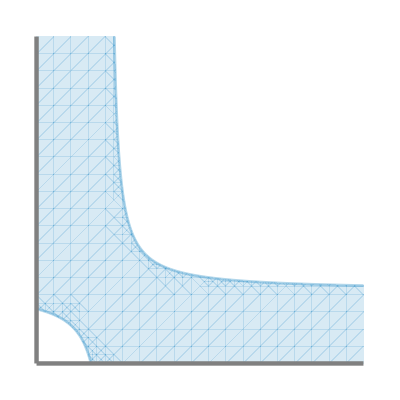

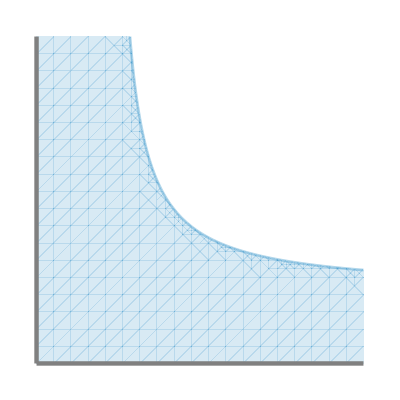

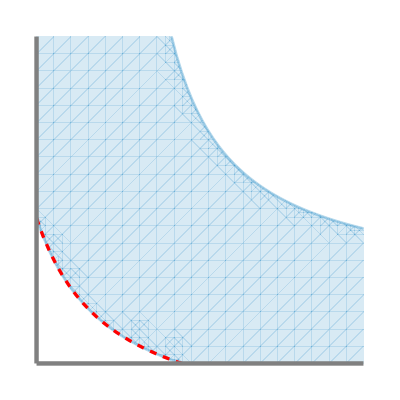

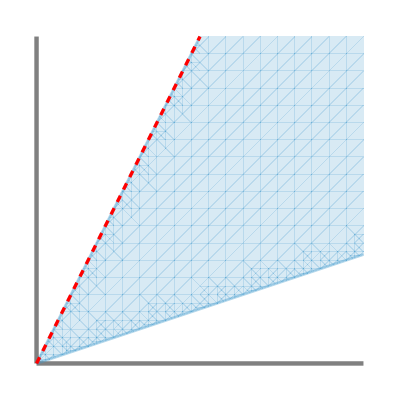

```mathematica
dir="C://bboros//Dropbox//disguised_toric//figures//";
disgκ=(1-Subscript[κ, 6]/Subscript[κ, 1])(1-Subscript[κ, 5]/Subscript[κ, 3])<=(Subscript[κ, 2] Subscript[κ, 4])/(Subscript[κ, 1] Subscript[κ, 3])<=(1+Subscript[κ, 6]/Subscript[κ, 1])(1+Subscript[κ, 5]/Subscript[κ, 3]);
b=4.5;
xaxis=ListLinePlot[{{0,0},{b,0}},PlotStyle->{Gray,Thickness[0.008]}];
yaxis=ListLinePlot[{{0,0},{0,b}},PlotStyle->{Gray,Thickness[0.008]}];

(* case  *)
κspec={Subscript[κ, 1]->1,Subscript[κ, 3]->1,Subscript[κ, 2]->1,Subscript[κ, 4]->1/4};
rgnpl=RegionPlot[disgκ/.κspec,{Subscript[κ, 5],0,b},{Subscript[κ, 6],0,b},PlotStyle->{Opacity[0.2]},GridLines->Automatic,BoundaryStyle->None,Frame->False,PlotRange->{{0,b},{0,b}}];
dt1=Plot[1-(Subscript[κ, 2] Subscript[κ, 4])/(Subscript[κ, 1] Subscript[κ, 3])/(1-Subscript[κ, 5]/Subscript[κ, 3])/.κspec,{Subscript[κ, 5],0,1},PlotRange->{{0,1},{0,1}},PlotStyle->{Opacity[0.4],Thickness[0.005]}];
dt2=Plot[1-(Subscript[κ, 2] Subscript[κ, 4])/(Subscript[κ, 1] Subscript[κ, 3])/(1-Subscript[κ, 5]/Subscript[κ, 3])/.κspec,{Subscript[κ, 5],1,b},PlotRange->{{0,b},{0,b}},PlotStyle->{Opacity[0.4],Thickness[0.005]}];
shw=Show[rgnpl,dt1,dt2,xaxis,yaxis]
Export[dir<>"running_k4_small.png",shw];

(* case  *)
κspec={Subscript[κ, 1]->1,Subscript[κ, 3]->1,Subscript[κ, 2]->1,Subscript[κ, 4]->1};
rgnpl=RegionPlot[disgκ/.κspec,{Subscript[κ, 5],0,b},{Subscript[κ, 6],0,b},PlotStyle->{Opacity[0.2]},GridLines->Automatic,BoundaryStyle->None,Frame->False,PlotRange->{{0,b},{0,b}}];
dt=Plot[1-(Subscript[κ, 2] Subscript[κ, 4])/(Subscript[κ, 1] Subscript[κ, 3])/(1-Subscript[κ, 5]/Subscript[κ, 3])/.κspec,{Subscript[κ, 5],1,b},PlotRange->{{0,b},{0,b}},PlotStyle->{Opacity[0.4],Thickness[0.005]}];
shw=Show[rgnpl,dt,xaxis,yaxis]
Export[dir<>"running_k4_equal.png",shw];


(* case  *)
κspec={Subscript[κ, 1]->1,Subscript[κ, 3]->1,Subscript[κ, 2]->1,Subscript[κ, 4]->3};
rgnpl=RegionPlot[disgκ/.κspec,{Subscript[κ, 5],0,b},{Subscript[κ, 6],0,b},PlotStyle->{Opacity[0.2]},GridLines->Automatic,BoundaryStyle->None,Frame->False,PlotRange->{{0,b},{0,b}}];
dt1=Plot[1-(Subscript[κ, 2] Subscript[κ, 4])/(Subscript[κ, 1] Subscript[κ, 3])/(1-Subscript[κ, 5]/Subscript[κ, 3])/.κspec,{Subscript[κ, 5],1,b},PlotRange->{{0,b},{0,b}},PlotStyle->{Opacity[0.4],Thickness[0.005]}];
dt2=Plot[(Subscript[κ, 2] Subscript[κ, 4])/(Subscript[κ, 1] Subscript[κ, 3])/(1+Subscript[κ, 5]/Subscript[κ, 3])-1/.κspec,{Subscript[κ, 5],0,b},PlotRange->{{0,b},{0,b}},PlotStyle->{Opacity[0.4],Thickness[0.005]}];
toric=Plot[(Subscript[κ, 2] Subscript[κ, 4])/(Subscript[κ, 1] Subscript[κ, 3])/(1+Subscript[κ, 5]/Subscript[κ, 3])-1/.κspec,{Subscript[κ, 5],0,b},PlotRange->{{0,b},{0,b}},PlotStyle->{Red,Dashed,Thickness[0.006]}];
shw=Show[rgnpl,dt1,dt2,toric,xaxis,yaxis]
Export[dir<>"running_k4_big.png",shw];

(* flux cone *)
b=6.5;
xaxis=ListLinePlot[{{0,0},{b,0}},PlotStyle->{Gray,Thickness[0.008]}];
yaxis=ListLinePlot[{{0,0},{0,b}},PlotStyle->{Gray,Thickness[0.008]}];
rgnpl=RegionPlot[Abs[Subscript[β, 4]-Subscript[β, 1]]<=Subscript[β, 1]<=Subscript[β, 4]+(Subscript[β, 1]+Subscript[β, 4])/2,{Subscript[β, 1],0,b},{Subscript[β, 4],0,b},PlotStyle->{Opacity[0.2]},GridLines->Automatic,BoundaryStyle->None,Frame->False,PlotRange->{{0,b},{0,b}}];
dt1=Plot[2 Subscript[β, 1],{Subscript[β, 1],0,b},PlotRange->{{0,b},{0,b}},PlotStyle->{Opacity[0.4],Thickness[0.005]}];
dt2=Plot[1/3 Subscript[β, 1],{Subscript[β, 1],0,b},PlotRange->{{0,b},{0,b}},PlotStyle->{Opacity[0.4],Thickness[0.005]}];
toric=Plot[2 Subscript[β, 1],{Subscript[β, 1],0,b},PlotRange->{{0,b},{0,b}},PlotStyle->{Red,Dashed,Thickness[0.006]}];
shw=Show[rgnpl,xaxis,yaxis,dt1,dt2,toric]
Export[dir<>"running_flux.png",shw];
```

## 7.3 Reversible LVA

```mathematica
rxnG={{2,0}->{3,0},{3,0}->{2,0},{1,1}->{0,2},{0,2}->{1,1},{0,1}->{0,0},{0,0}->{0,1}};
DrawEGraph[rxnG][[1]]
```

-Graphics-

### Five positive equilibria

```mathematica
f=GetMassAction[rxnG][[1]];
κsubst={Subscript[κ, 1]->2,Subscript[κ, 2]->1/10,Subscript[κ, 3]->3,Subscript[κ, 4]->1,Subscript[κ, 5]->3,Subscript[κ, 6]->1};
eqs=N[Solve[(f/.κsubst)==0&&{x,y}>0,{x,y}]]
J=D[f,{{x,y}}];
Eigenvalues/@(J/.κsubst/.eqs)
```

{{x→0.175311,y→0.353643},{x→0.601603,y→0.56736},{x→0.781398,y→0.724485},{x→4.28929,y→9.96818},{x→14.1262,y→39.4038}}

{{-3.24818,-0.302082},{-1.86674,0.132589},{-1.01267,-0.323142},{-29.2734,0.938091},{-157.916,-3.08462}}

## 7.4 A network with a subcritical Bogdanov-Takens bifurcation

```mathematica
rxnG={{1,0}->{0,0},{0,0}->{1,1},{1,1}->{2,0},{2,0}->{3,0},{3,0}->{2,0}};
DrawEGraph[rxnG][[1]]
```

-Graphics-

### Three positive equilibria

```mathematica
f=GetMassAction[rxnG][[1]];
κsubst={Subscript[κ, 1]->7,Subscript[κ, 2]->1,Subscript[κ, 3]->2,Subscript[κ, 4]->7,Subscript[κ, 5]->2};
eqs=N[Solve[(f/.κsubst)==0&&{x,y}>0,{x,y}]]
J=D[f,{{x,y}}];
Eigenvalues/@(J/.κsubst/.eqs)
```

{{x→0.5,y→1.},{x→1.,y→0.5},{x→2.,y→0.25}}

{{-0.25+1.19896 ⅈ,-0.25-1.19896 ⅈ},{-1.41421,1.41421},{-3.25+1.19896 ⅈ,-3.25-1.19896 ⅈ}}

### Disguised toric locus

```mathematica
Resolve[Exists[{x,y},f==0&&x<=Subscript[κ, 2]/Subscript[κ, 1]&&{x,y}>0&&{Subscript[κ, 1],Subscript[κ, 2],Subscript[κ, 3],Subscript[κ, 4],Subscript[κ, 5]}>0]]
```

κ_1>0&&κ_2>0&&κ_4>0&&κ_5≥(κ_1^3+κ_1 κ_2 κ_4)/κ_2^2&&κ_3>0

How much of the simplex is covered by the disguised toric locus? We get approximately 35.4%
(5 million simulations take about 1 minute.)

```mathematica
M=5000000;
count=0;
disgκ=Subscript[κ, 5]/Subscript[κ, 1]>=(Subscript[κ, 1]/Subscript[κ, 2])^2+Subscript[κ, 4]/Subscript[κ, 2];
For[i=1,i<=M,i++,{
rnd=RandomVariate[ExponentialDistribution[1],5];
If[disgκ/.Table[Subscript[κ, j]->rnd[[j]],{j,1,5}],count++];
}];
Print[N[100count/M,3],"% of the simplex is covered by K^dt(G)"];
```

35.4% of the simplex is covered by K^dt(G)

## 7.6 Tetrahedron

```mathematica
rxnG={{0,0,0}->{1,0,0},{1,0,0}->{0,0,0},{1,0,0}->{2,0,0},{2,0,0}->{1,0,0},{1,0,0}->{0,1,1},{0,1,1}->{1,0,0},{0,2,0}->{0,1,1},{0,1,1}->{0,2,0},{0,1,1}->{0,0,2},{0,0,2}->{0,1,1}};
```

### Disguised toric flux cone

```mathematica
{DE,VB}=GetDEandVB[rxnG,rxnG];
sol=Solve[DE&&VB,{Subscript[β, 2],Subscript[β, 5],Subscript[β, 8],Subscript[γ, 1],Subscript[γ, 2],Subscript[γ, 3],Subscript[γ, 4],Subscript[γ, 5],Subscript[γ, 6],Subscript[γ, 7],Subscript[γ, 8],Subscript[γ, 9],Subscript[γ, 10]}][[1]];
MatrixForm[sol]
```

(β_2→β_1+β_3-β_4
β_5→β_6
β_8→β_7+β_9-β_10
γ_1→β_1
γ_2→β_1
γ_3→β_4
γ_4→β_4
γ_5→β_6
γ_6→β_6
γ_7→β_7
γ_8→β_7
γ_9→β_10
γ_10→β_10)

## 7.7 A four-dimensional example

```mathematica
rxnG={{0,0,0,0}->{1,0,0,0},{1,0,0,0}->{0,0,0,0},{0,0,0,0}->{0,1,0,0},{0,1,0,0}->{0,0,0,0},{0,0,0,0}->{0,0,1,0},{0,0,1,0}->{0,0,0,0},{0,0,0,0}->{0,0,0,1},{0,0,0,1}->{0,0,0,0},{0,0,0,1}->{2,0,0,0},{2,0,0,0}->{0,0,0,1},{0,0,0,1}->{0,2,0,0},{0,2,0,0}->{0,0,0,1},{0,0,0,1}->{0,0,2,0},{0,0,2,0}->{0,0,0,1}};
```

### Equilibrium fluxes

```mathematica
EQ=GetEQ[rxnG]
```

{β_1-β_2+2 β_9-2 β_10,β_3-β_4+2 β_11-2 β_12,β_5-β_6+2 β_13-2 β_14,β_7-β_8-β_9+β_10-β_11+β_12-β_13+β_14}==0

### Disguised toric flux cone

```mathematica
rxnH=Join[rxnG,{{1,0,0,0}->{2,0,0,0},{0,1,0,0}->{0,2,0,0},{0,0,1,0}->{0,0,2,0},{0,0,0,1}->{1,0,0,0},{0,0,0,1}->{0,1,0,0},{0,0,0,1}->{0,0,1,0}}];
{DE,VB}=GetDEandVB[rxnG,rxnH];
sol=Solve[DE&&VB,{Subscript[β, 8],Subscript[β, 9],Subscript[β, 11],Subscript[β, 13],Subscript[γ, 1],Subscript[γ, 3],Subscript[γ, 5],Subscript[γ, 7],Subscript[γ, 8],Subscript[γ, 9],Subscript[γ, 10],Subscript[γ, 11],Subscript[γ, 12],Subscript[γ, 13],Subscript[γ, 14],Subscript[γ, 15],Subscript[γ, 16],Subscript[γ, 17],Subscript[γ, 18],Subscript[γ, 19],Subscript[γ, 20]}][[1]];
MatrixForm[sol]
```

(β_8→1/2 (β_1-β_2+β_3-β_4+β_5-β_6+2 β_7)
β_9→1/2 (-β_1+β_2+2 β_10)
β_11→1/2 (-β_3+β_4+2 β_12)
β_13→1/2 (-β_5+β_6+2 β_14)
γ_1→β_1
γ_3→β_3
γ_5→β_5
γ_7→β_7
γ_8→β_1+β_3+β_5+β_7-γ_2-γ_4-γ_6
γ_9→β_2+β_10-γ_2
γ_10→β_10
γ_11→β_4+β_12-γ_4
γ_12→β_12
γ_13→β_6+β_14-γ_6
γ_14→β_14
γ_15→-β_2+γ_2
γ_16→-β_4+γ_4
γ_17→-β_6+γ_6
γ_18→-β_1-β_2+2 γ_2
γ_19→-β_3-β_4+2 γ_4
γ_20→-β_5-β_6+2 γ_6)

Hence, , ,  in order to guarantee .
With , , , we have , , , all positive.
Hence, the only thing we still need is that , which leads to the condition
.

How much of the simplex is covered by the disguised toric locus? We get approximately 62.6%
We have an explicit formula for the disguised toric flux cone, but not for the disguised toric locus.
Hence, for a given rate constant, we solve numerically for the (unique) positive equilibrium, and then compute the corresponding flux.
(100k simulations take about 25 minutes, because solving for the positive equilibrium is slow.)
We got 62.70%, 62.30%, 62.77%, 62.49%, 62.43%, 62.98%, 62.40%, 62.38%, 62.58%, 62.77% for different runs of 100k simulations, a total of 1 million runs, the average is 62.6%.

```mathematica
{f,monomials}=GetMassAction[rxnG][[{1,4}]];
M=10000;
count=0;
disgβ=Subscript[β, 1]-Max[Subscript[β, 2],(Subscript[β, 1]+Subscript[β, 2])/2]+Subscript[β, 3]-Max[Subscript[β, 4],(Subscript[β, 3]+Subscript[β, 4])/2]+Subscript[β, 5]-Max[Subscript[β, 6],(Subscript[β, 5]+Subscript[β, 6])/2]+Subscript[β, 7]>=0;
For[i=1,i<=M,i++,{
rnd=RandomVariate[ExponentialDistribution[1],14];
κsubst=Table[Subscript[κ, j]->rnd[[j]],{j,1,14}];
ff=f/.κsubst;
equil=NSolve[ff==0&&x>0&&y>0&&z>0&&w>0,{x,y,z,w}][[1]];
monomspec=monomials[[1;;7]]/.κsubst/.equil;
βsubst=Table[Subscript[β, j]->monomspec[[j]],{j,1,7}];
If[disgβ/.βsubst,count++];
}];
Print[N[100count/M,3],"% of the simplex is covered by K^dt(G) (based on ",M," simulations)"];
```

62.3% of the simplex is covered by K^dt(G) (based on 10000 simulations)

## Appendix

We briefly explain how to sample uniformly from the simplex .
Lemma Let Exponential() be independent random variables. Let  (). Then  is uniformly distributed on the simplex.
Proof Let  and . Then the Jacobian determinant of  equals . Hence, the joint density function of  is  for . Note that this function is independent of . By integration w.r.t. , find that the joint density function of  is constant  over the simplex. This concludes the proof.
Remark Since the equilibrium of a mass-action doesn’t depend on scaling of the rate constants, in practice we don’t need to divide by the sum. Also, notice that the parameter  of the exponential distribution has no effect on the joint distribution of  (which is also called Dirichlet(1,...,1) distribution).